# Testing out DMFormFactor functions

```mathematica
<<"v6/dmformfactor-V6.m";
```

Welcome to DMFormFactor version 1.1.

Functions are SetCoeffsNonrel, SetCoeffsRel, SetCoeffsNucl, ZeroCoeffs, SetJChi, SetMchi, SetIsotope, SetHALO, SetHelm, TransitionProbability, ResponseNucl, DiffCrossSection, ApproxTotalCrossSection, and EventRate.

## Event rate

Model setup

```mathematica
(* Model Setup *)
SetJChi[1/2](* WIMP spin *)
SetMChi[MWIMP] (* WIMP mass *)
Xe131filename="default";  (* nuclear density matrix (using default density matrices) *)
bFM="default"; (* oscillation parameter (default: approximate formulae used) *)
SetIsotope[54,131,bFM,Xe131filename] (*[Z,A,bFM,filename]*)
(*SetCoeffsNonrel[3,3.1,"p"](* Set non-zero NR EFT coefficient values *)
*)
SetCoeffsRel[1,2fp,0]
fp=2.4*10^(-4);
```

Getting default matrix...

Setting isotope to xenon-131.

Relativistic Operator 1 is χ̄χN̄N

Matrix elements

```mathematica
TransitionProbability[v,qGeV](* Spin-averaged matrix element squared *)
```

Your Lagrangian is

L_prot=(3.95945×10^-9 χ̄χN̄N)/GeV^2

L_neut=(3.95945×10^-9 χ̄χN̄N)/GeV^2

Your transition probability is

1/GeV^4 ⅇ^(-67.4762 qGeV^2) (2.69015×10^-13-3.62113×10^-11 qGeV^2+1.92276×10^-9 qGeV^4-5.23867×10^-8 qGeV^6+8.08968×10^-7 qGeV^8-7.35075×10^-6 qGeV^10+0.000039221 qGeV^12-0.000117443 qGeV^14+0.000175642 qGeV^16-0.0000994134 qGeV^18+0.0000184195 qGeV^20)

```mathematica
TransitionProbability[v,qGeV,True] (* as above, with relativistic normalisation *)
```

Your Lagrangian is

L_prot=0.+(0.0000545076 ⅈ S_N·(q×v^⊥))/GeV^3

L_neut=0.

Your transition probability is

ⅇ^(-39.8764 qGeV^2) qGeV^2 (-0.393037 qGeV^10+0.00852433 v^2+qGeV^6 (0.0134931-81.4917 v^2)+qGeV^2 (0.00040821-0.456613 v^2)+qGeV^4 (-0.00604702+9.15739 v^2)+qGeV^8 (0.117966+271.513 v^2))

Differential cross section per recoil
energy

```mathematica
DiffCrossSection[]
```

Attempting to compute a recoil spectrum...

```mathematica
(* Parameters *)
mNucleon=0.938 GeV;
NT=1/(131 mNucleon);(*Number of target nuclei per detector mass*)
Centimeter=(10^13 Femtometer);
rhoDM=0.3 GeV/Centimeter^3;(*Local dark matter density*)
ve=232 KilometerPerSecond;(*Earth's velocity in galactic rest frame*)
v0=220 KilometerPerSecond;(*Mean WIMP speed in galactic rest frame*)
SetHALO["MB"];(*using default MB Halo*)
```

```mathematica
(* Switch to cutoff MB Halo *)
vesc=550 KilometerPerSecond;
SetHALO["MBcutoff"];
```

```mathematica
dEdR=EventRate[NT,rhoDM,qGeV,ve,v0]
```

Your Lagrangian is

L_prot=χ̄χN̄N (0.+(3.95945×10^-9)/GeV^2)

L_neut=χ̄χN̄N (0.+(3.95945×10^-9)/GeV^2)

Your event rate is

1/MWIMP^3 2.6053×10^-44 GeV^2 (0.+646.112 ⅇ^(-67.4762 qGeV^2) (0.+(0.+14.0857 (0.+(3.95945×10^-9)/GeV^2)^2 GeV^2 MWIMP^2) (2915.98-354651. qGeV^2+1.66663×10^7 qGeV^4-3.89909×10^8 qGeV^6+4.97028×10^9 qGeV^8-3.52778×10^10 qGeV^10+1.35444×10^11 qGeV^12-2.55168×10^11 qGeV^14+1.83904×10^11 qGeV^16-134154. qGeV^18+0.0248999 qGeV^20)+2 (0.+14.0857 (0.+(3.95945×10^-9)/GeV^2)^2 GeV^2 MWIMP^2) (4157.7-551594. qGeV^2+2.86787×10^7 qGeV^4-7.57984×10^8 qGeV^6+1.12026×10^10 qGeV^8-9.54998×10^10 qGeV^10+4.63347×10^11 qGeV^12-1.19651×10^12 qGeV^14+1.39184×10^12 qGeV^16-4.64714×10^11 qGeV^18+170015. qGeV^20)+(0.+14.0857 (0.+(3.95945×10^-9)/GeV^2)^2 GeV^2 MWIMP^2) (5928.2-851956. qGeV^2+4.86226×10^7 qGeV^4-1.43569×10^9 qGeV^6+2.42258×10^10 qGeV^8-2.42602×10^11 qGeV^10+1.43964×10^12 qGeV^12-4.84312×10^12 qGeV^14+8.236×10^12 qGeV^16-5.41182×10^12 qGeV^18+1.17492×10^12 qGeV^20)) (Erf[1.05455-(5.54336 (122.914 GeV+MWIMP) qGeV)/MWIMP]+Erf[1.05455+(5.54336 (122.914 GeV+MWIMP) qGeV)/MWIMP]))

```mathematica
fdEdR[q_]:=Simplify[dEdR/.{qGeV->q},GeV>0]
```

```mathematica
fdEdR[x]
```

1/MWIMP 4.36737×10^-45 ⅇ^(-67.4762 x^2) (1.46049×10^-8-1.96592×10^-6 x^2+0.000104387 x^4-0.00284409 x^6+0.0439191 x^8-0.399075 x^10+2.12932 x^12-6.37604 x^14+9.53564 x^16-5.39718 x^18+1. x^20) (Erf[1.05455+(-5.54336-(681.355 GeV)/MWIMP) x]+Erf[1.05455+(5.54336+(681.355 GeV)/MWIMP) x])

```mathematica
fdEdR[0.1]GeV*2500KilogramDay
```

1/MWIMP 1.84085×10^59 GeV (6.54292×10^-54 Erf[0.500209-(68.1355 GeV)/MWIMP]+6.54292×10^-54 Erf[1.60888+(68.1355 GeV)/MWIMP])

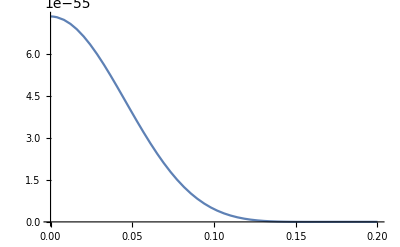

```mathematica
Plot[fdEdR[q]GeV/.MWIMP->(150GeV),{q,0,0.2}]
```

Total predicted number of events for 150 GeV WIMP

```mathematica
2500KilogramDay*NIntegrate[fdEdR[qGeV] GeV*(qGeV GeV/(131 mNucleon))/.MWIMP->(150GeV),{qGeV,0,10}]
```

2.04862

Total predicted number of events as function of WIMP mass

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

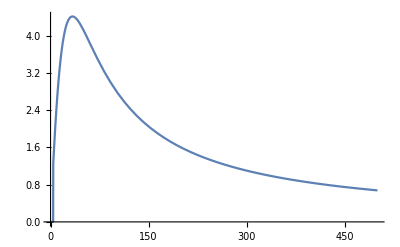

```mathematica
Plot[2500KilogramDay*NIntegrate[fdEdR[qGeV] GeV*(qGeV GeV/(131 mNucleon))/.MWIMP->(M GeV),{qGeV,0,10}],{M,0,500}]
```